```mathematica
Series[E[-α*x],{x,1,6}]
```

ⅇ[-α]+O[x-1]^7

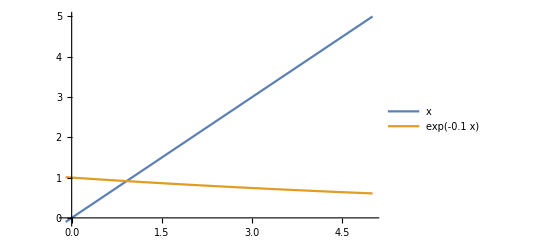

```mathematica
Plot[{x, Exp[-0.1*x]}, {x, -0.1,05},PlotLegends->"Expressions"]
```

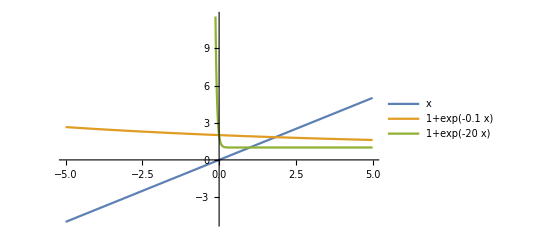

```mathematica
Plot[{x, 1+Exp[-0.1x],1+Exp[-20*x]},{x,-5,5},PlotLegends->"Expressions"]
```

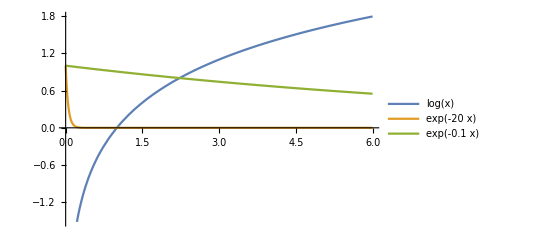

```mathematica
Plot[{Log[x] ,Exp[-20*x], Exp[-0.1*x]}, {x, 0, 6},PlotLegends->"Expressions"]
```

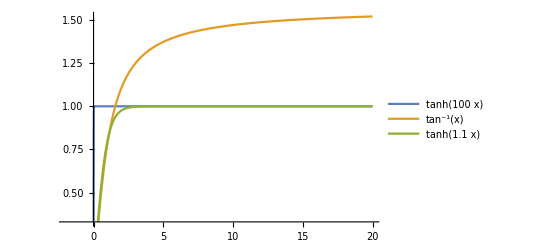

```mathematica
Plot[{Tanh[100*x], ArcTan[x],Tanh[1.1*x]},{x,-2,20},PlotLegends->"Expressions"]
```

```mathematica
0
```

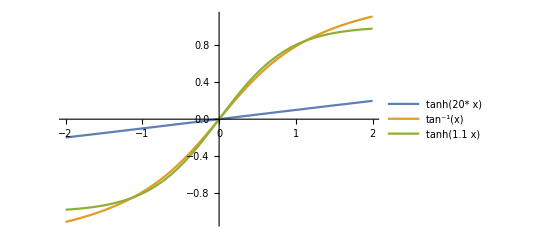

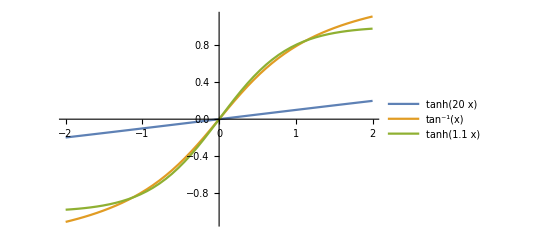

```mathematica
Series[1+Exp[-y],{y,0,3}]
```

2-y+y^2/2-y^3/6+O[y]^4

```mathematica
Series[Exp[-y],{y,0,3}]
```

1-y+y^2/2-y^3/6+O[y]^4

```mathematica
Series[Tanh[a*x],{x,0,5}]
```

a x-(a^3 x^3)/3+(2 a^5 x^5)/15+O[x]^6

```mathematica
Series[ArcTan[x],{x,0,5}]
```

x-x^3/3+x^5/5+O[x]^6

```mathematica
Derivative[ArcTan[x],x]
```

Derivative[ArcTan[x],x]

```mathematica
Series[ArcTan[Tan[1]+x],{x,0,2}]
```

1+x/(1+Tan[1]^2)-(Tan[1] x^2)/((1+Tan[1]^2)^2)+O[x]^3

```mathematica
Series[Log[1+x],{x,0,3}]
```

x-x^2/2+x^3/3+O[x]^4

```mathematica
-a^3*y+y
```

y-a^3 y

```mathematica
Simplify[y-2 a^3 y]
```

y-2 a^3 y

```mathematica
((-a^3-1)/3)^2
```

1/9 (-1-a^3)^2

```mathematica
Solve[a*x-(a^3*x^3)/3+(2*a^5*x^5)/15==x-x^3/3+x^5/5,x]
```

{{x→0},{x→-(√(-5/(-3+2 a^5)+(5 a^3)/(-3+2 a^5)-(√5 √(-31+36 a-10 a^3+24 a^5-19 a^6))/(-3+2 a^5)))/(√2)},{x→(√(-5/(-3+2 a^5)+(5 a^3)/(-3+2 a^5)-(√5 √(-31+36 a-10 a^3+24 a^5-19 a^6))/(-3+2 a^5)))/(√2)},{x→-(√(-5/(-3+2 a^5)+(5 a^3)/(-3+2 a^5)+(√5 √(-31+36 a-10 a^3+24 a^5-19 a^6))/(-3+2 a^5)))/(√2)},{x→(√(-5/(-3+2 a^5)+(5 a^3)/(-3+2 a^5)+(√5 √(-31+36 a-10 a^3+24 a^5-19 a^6))/(-3+2 a^5)))/(√2)}}

```mathematica
Solve[a-(a^3*y)/3+(2*a^5*y^2)/15==1-y/3+y/5,y]
```

{{y→(-2+5 a^3-√(4-20 a^3+120 a^5-95 a^6))/(4 a^5)},{y→(-2+5 a^3+√(4-20 a^3+120 a^5-95 a^6))/(4 a^5)}}